```mathematica
solAnalytic[r]//Simplify
```

-(2 √π (-r+(-5+r) HeavisideTheta[-5+r]))/(5 r)

```mathematica
solAnalytic1[r]
```

-(2 (-√(3 π) r^3-125 √(3 π) HeavisideTheta[-5+r]+√(3 π) r^3 HeavisideTheta[-5+r]))/(75 r^2)

```mathematica
D[solAnalytic[r],r]//Simplify
```

-(2 √π HeavisideTheta[-5+r])/r^2

```mathematica
D[solAnalytic[r],{r,2}]//Simplify
```

-2/5 √π (1/5 DiracDelta[-5+r]-(10 HeavisideTheta[-5+r])/r^3)

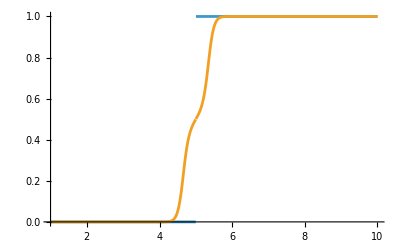

```mathematica
Plot[{Re[HLog[r,5]],Re[HLog[γ[r],5]]},{r,1,10}]
```

```mathematica
solNumericIn[r_]:=solAnalytic[r]HeavisideTheta[5-r]
```

```mathematica
solNumericOut[r_]:=solAnalytic[r]HeavisideTheta[r-5]
```

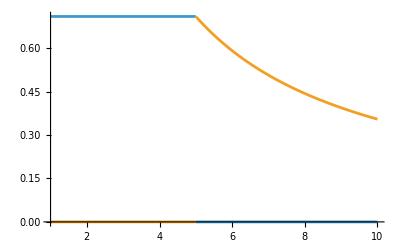

```mathematica
Plot[{solNumericIn[r],solNumericOut[r]},{r,1,10}]
```

```mathematica
solNumericInCont[r_]:=solAnalytic[r]HeavisideTheta[5-Re[r]](1-HLog[r,5])
```

```mathematica
solNumericOutCont[r_]:=solAnalytic[r]HeavisideTheta[Re[r]-5]HLog[r,5]
```

Won’t work when using the numeric solution because the numeric solution also need to extend into the complex domain.

```mathematica
Plot[{Re@solNumericInCont[r],Re@solNumericOutCont[r]},{r,1,10}]
```

-Graphics-

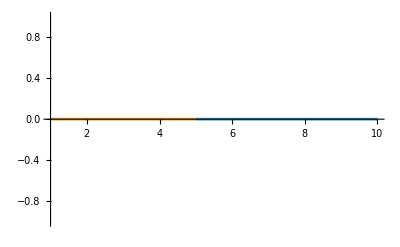

```mathematica
Plot[{Re@solNumericInCont[γ[r]],Re@solNumericOutCont[γ[r]]},{r,1,10}]
```

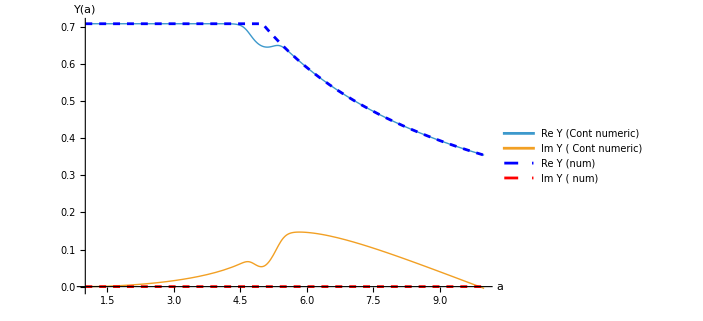

```mathematica
Plot[{Re[solNumericCont3[a]],Im[solNumericCont3[a]],Re[solNumeric[a]],Im[solNumeric[a]]},{a,1,10},PlotLegends->{"Re Y (Cont numeric)","Im Y ( Cont numeric)","Re Y (num)","Im Y ( num)"},AxesLabel->{"a","Y(a)"},PlotRange->All,ImageSize->520,PlotStyle->{{Thick},{Thick},{Dashed,Blue},{Dashed,Red}   }]
```